C:\Users\danie\Desktop\TESIS\Campo escalar en frontera θ

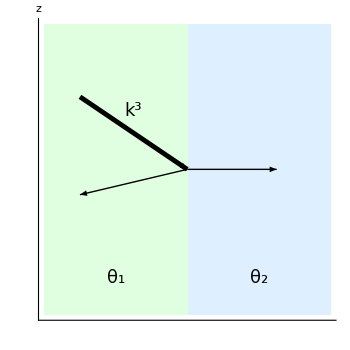

ingoing_L.png

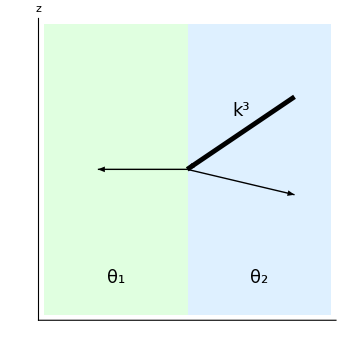

ingoing_R.png

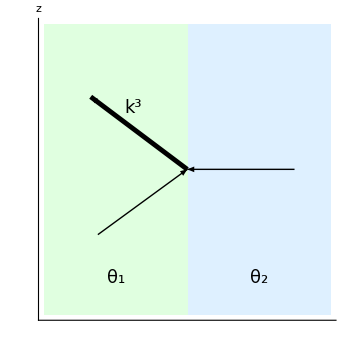

outgoing_L.png

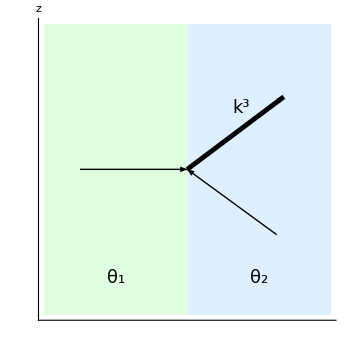

outgoing_R.png

```mathematica
SetDirectory[NotebookDirectory[]]
ingoingL=Show[RegionPlot[x>0,{x,-4,4},{y,-4,4},PlotRange->All,PlotStyle->LightBlue,BoundaryStyle->None],
RegionPlot[x<0,{x,-4,4},{y,-4,4},PlotRange->All,PlotStyle->LightGreen,BoundaryStyle->None],
Graphics[{Thickness[0.01],Arrow[{{-3,2},{0,0}}]}],
Graphics[Arrow[{{0,0},{2.5,0}}]],
Graphics[Arrow[{{0,0},{-3,-0.7}}]],
Epilog->{Text[Style[Subscript[θ,1],18],{-2,-3}],Text[Style[Subscript[θ,2],18],{2,-3}],Text[Style[Superscript[k,3],18],{-1.5,1.6}]},
AxesStyle->Black,ImageSize->350, PlotRange->All,Frame->None,Axes->{False,True},Ticks->None,AxesLabel->{None,Style["z",18]}
]
Export["ingoing_L.png",ingoingL,ImageResolution->600]
ingoingR=Show[RegionPlot[x>0,{x,-4,4},{y,-4,4},PlotRange->All,PlotStyle->LightBlue,BoundaryStyle->None],
RegionPlot[x<0,{x,-4,4},{y,-4,4},PlotRange->All,PlotStyle->LightGreen,BoundaryStyle->None],
Graphics[{Thickness[0.01],Arrow[{{3,2},{0,0}}]}],
Graphics[Arrow[{{0,0},{-2.5,0}}]],
Graphics[Arrow[{{0,0},{3,-0.7}}]],
Epilog->{Text[Style[Subscript[θ,1],18],{-2,-3}],Text[Style[Subscript[θ,2],18],{2,-3}],Text[Style[Superscript[k,3],18],{1.5,1.6}]},
AxesStyle->Black,ImageSize->350, PlotRange->All,Frame->None,Axes->{False,True},Ticks->None,AxesLabel->{None,Style["z",18]}
]
Export["ingoing_R.png",ingoingR,ImageResolution->600]
outgoingL=Show[RegionPlot[x>0,{x,-4,4},{y,-4,4},PlotRange->All,PlotStyle->LightBlue,BoundaryStyle->None],
RegionPlot[x<0,{x,-4,4},{y,-4,4},PlotRange->All,PlotStyle->LightGreen,BoundaryStyle->None],
Graphics[{Thickness[0.01],Arrow[{{0,0},{-2.7,2}}]}],
Graphics[Arrow[{{3,0},{0,0}}]],
Graphics[Arrow[{{-2.5,-1.8},{0,0}}]],
Epilog->{Text[Style[Subscript[θ,1],18],{-2,-3}],Text[Style[Subscript[θ,2],18],{2,-3}],Text[Style[Superscript[k,3],18],{-1.5,1.7}]},
AxesStyle->Black,ImageSize->350, PlotRange->All,Frame->None,Axes->{False,True},Ticks->None,AxesLabel->{None,Style["z",18]}
]
Export["outgoing_L.png",outgoingL,ImageResolution->600]
outgoingR=Show[RegionPlot[x>0,{x,-4,4},{y,-4,4},PlotRange->All,PlotStyle->LightBlue,BoundaryStyle->None],
RegionPlot[x<0,{x,-4,4},{y,-4,4},PlotRange->All,PlotStyle->LightGreen,BoundaryStyle->None],
Graphics[{Thickness[0.01],Arrow[{{0,0},{2.7,2}}]}],
Graphics[Arrow[{{-3,0},{0,0}}]],
Graphics[Arrow[{{2.5,-1.8},{0,0}}]],
Epilog->{Text[Style[Subscript[θ,1],18],{-2,-3}],Text[Style[Subscript[θ,2],18],{2,-3}],Text[Style[Superscript[k,3],18],{1.5,1.7}]},
AxesStyle->Black,ImageSize->350, PlotRange->All,Frame->None,Axes->{False,True},Ticks->None,AxesLabel->{None,Style["z",18]}
]
Export["outgoing_R.png",outgoingR,ImageResolution->600]
```